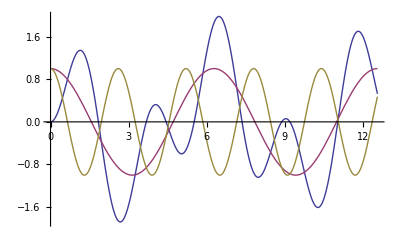

```mathematica
Plot[{Cos[x]-Cos[x (1+Sqrt[2])], Cos[x], Cos[x (1+Sqrt[2])]},{x,0,4Pi}]
```

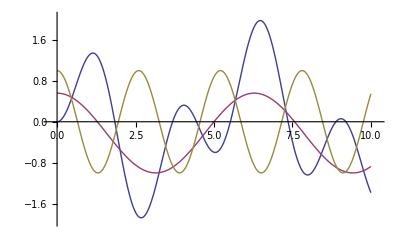

```mathematica
Tuples[{2,1,0}, 3]
```

{{2,2,2},{2,2,1},{2,2,0},{2,1,2},{2,1,1},{2,1,0},{2,0,2},{2,0,1},{2,0,0},{1,2,2},{1,2,1},{1,2,0},{1,1,2},{1,1,1},{1,1,0},{1,0,2},{1,0,1},{1,0,0},{0,2,2},{0,2,1},{0,2,0},{0,1,2},{0,1,1},{0,1,0},{0,0,2},{0,0,1},{0,0,0}}

```mathematica
show[{x}, {x,1,100}]
```

```mathematica
NestList[#+1&, 1,10 ]
```

{1,2,3,4,5,6,7,8,9,10,11}

```mathematica
With[{k=2, m=8}, Table[FromDigits[Reverse[IntegerDigits[n,k,m]], k],{n,0,(k^m)-1}]]
```

{0,128,64,192,32,160,96,224,16,144,80,208,48,176,112,240,8,136,72,200,40,168,104,232,24,152,88,216,56,184,120,248,4,132,68,196,36,164,100,228,20,148,84,212,52,180,116,244,12,140,76,204,44,172,108,236,28,156,92,220,60,188,124,252,2,130,66,194,34,162,98,226,18,146,82,210,50,178,114,242,10,138,74,202,42,170,106,234,26,154,90,218,58,186,122,250,6,134,70,198,38,166,102,230,22,150,86,214,54,182,118,246,14,142,78,206,46,174,110,238,30,158,94,222,62,190,126,254,1,129,65,193,33,161,97,225,17,145,81,209,49,177,113,241,9,137,73,201,41,169,105,233,25,153,89,217,57,185,121,249,5,133,69,197,37,165,101,229,21,149,85,213,53,181,117,245,13,141,77,205,45,173,109,237,29,157,93,221,61,189,125,253,3,131,67,195,35,163,99,227,19,147,83,211,51,179,115,243,11,139,75,203,43,171,107,235,27,155,91,219,59,187,123,251,7,135,71,199,39,167,103,231,23,151,87,215,55,183,119,247,15,143,79,207,47,175,111,239,31,159,95,223,63,191,127,255}

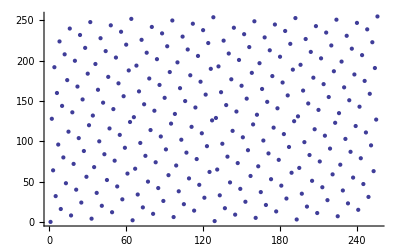

```mathematica
ListPlot[%145]
```

```mathematica
Permutations[{1,3,5,7}]
```

{{1,3,5,7},{1,3,7,5},{1,5,3,7},{1,5,7,3},{1,7,3,5},{1,7,5,3},{3,1,5,7},{3,1,7,5},{3,5,1,7},{3,5,7,1},{3,7,1,5},{3,7,5,1},{5,1,3,7},{5,1,7,3},{5,3,1,7},{5,3,7,1},{5,7,1,3},{5,7,3,1},{7,1,3,5},{7,1,5,3},{7,3,1,5},{7,3,5,1},{7,5,1,3},{7,5,3,1}}

```mathematica
Table[Prime[n],{n,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
Permutations[Table[Prime[n],{n,4}]]
```

Permutations[{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}]

```mathematica
Permutations[Table[Prime[n],{n,6}]]
```

{{2,3,5,7,11,13},{2,3,5,7,13,11},{2,3,5,11,7,13},{2,3,5,11,13,7},{2,3,5,13,7,11},{2,3,5,13,11,7},{2,3,7,5,11,13},{2,3,7,5,13,11},{2,3,7,11,5,13},{2,3,7,11,13,5},{2,3,7,13,5,11},{2,3,7,13,11,5},{2,3,11,5,7,13},{2,3,11,5,13,7},{2,3,11,7,5,13},{2,3,11,7,13,5},{2,3,11,13,5,7},{2,3,11,13,7,5},{2,3,13,5,7,11},{2,3,13,5,11,7},{2,3,13,7,5,11},{2,3,13,7,11,5},{2,3,13,11,5,7},{2,3,13,11,7,5},{2,5,3,7,11,13},{2,5,3,7,13,11},{2,5,3,11,7,13},{2,5,3,11,13,7},{2,5,3,13,7,11},{2,5,3,13,11,7},{2,5,7,3,11,13},{2,5,7,3,13,11},{2,5,7,11,3,13},{2,5,7,11,13,3},{2,5,7,13,3,11},{2,5,7,13,11,3},{2,5,11,3,7,13},{2,5,11,3,13,7},{2,5,11,7,3,13},{2,5,11,7,13,3},{2,5,11,13,3,7},{2,5,11,13,7,3},{2,5,13,3,7,11},{2,5,13,3,11,7},{2,5,13,7,3,11},{2,5,13,7,11,3},{2,5,13,11,3,7},{2,5,13,11,7,3},{2,7,3,5,11,13},{2,7,3,5,13,11},{2,7,3,11,5,13},{2,7,3,11,13,5},{2,7,3,13,5,11},{2,7,3,13,11,5},{2,7,5,3,11,13},{2,7,5,3,13,11},{2,7,5,11,3,13},{2,7,5,11,13,3},{2,7,5,13,3,11},{2,7,5,13,11,3},{2,7,11,3,5,13},{2,7,11,3,13,5},{2,7,11,5,3,13},{2,7,11,5,13,3},{2,7,11,13,3,5},{2,7,11,13,5,3},{2,7,13,3,5,11},{2,7,13,3,11,5},{2,7,13,5,3,11},{2,7,13,5,11,3},{2,7,13,11,3,5},{2,7,13,11,5,3},{2,11,3,5,7,13},{2,11,3,5,13,7},{2,11,3,7,5,13},{2,11,3,7,13,5},{2,11,3,13,5,7},{2,11,3,13,7,5},{2,11,5,3,7,13},{2,11,5,3,13,7},{2,11,5,7,3,13},{2,11,5,7,13,3},{2,11,5,13,3,7},{2,11,5,13,7,3},{2,11,7,3,5,13},{2,11,7,3,13,5},{2,11,7,5,3,13},{2,11,7,5,13,3},{2,11,7,13,3,5},{2,11,7,13,5,3},{2,11,13,3,5,7},{2,11,13,3,7,5},{2,11,13,5,3,7},{2,11,13,5,7,3},{2,11,13,7,3,5},{2,11,13,7,5,3},{2,13,3,5,7,11},{2,13,3,5,11,7},{2,13,3,7,5,11},{2,13,3,7,11,5},{2,13,3,11,5,7},{2,13,3,11,7,5},{2,13,5,3,7,11},{2,13,5,3,11,7},{2,13,5,7,3,11},{2,13,5,7,11,3},{2,13,5,11,3,7},{2,13,5,11,7,3},{2,13,7,3,5,11},{2,13,7,3,11,5},{2,13,7,5,3,11},{2,13,7,5,11,3},{2,13,7,11,3,5},{2,13,7,11,5,3},{2,13,11,3,5,7},{2,13,11,3,7,5},{2,13,11,5,3,7},{2,13,11,5,7,3},{2,13,11,7,3,5},{2,13,11,7,5,3},{3,2,5,7,11,13},{3,2,5,7,13,11},{3,2,5,11,7,13},{3,2,5,11,13,7},{3,2,5,13,7,11},{3,2,5,13,11,7},{3,2,7,5,11,13},{3,2,7,5,13,11},{3,2,7,11,5,13},{3,2,7,11,13,5},{3,2,7,13,5,11},{3,2,7,13,11,5},{3,2,11,5,7,13},{3,2,11,5,13,7},{3,2,11,7,5,13},{3,2,11,7,13,5},{3,2,11,13,5,7},{3,2,11,13,7,5},{3,2,13,5,7,11},{3,2,13,5,11,7},{3,2,13,7,5,11},{3,2,13,7,11,5},{3,2,13,11,5,7},{3,2,13,11,7,5},{3,5,2,7,11,13},{3,5,2,7,13,11},{3,5,2,11,7,13},{3,5,2,11,13,7},{3,5,2,13,7,11},{3,5,2,13,11,7},{3,5,7,2,11,13},{3,5,7,2,13,11},{3,5,7,11,2,13},{3,5,7,11,13,2},{3,5,7,13,2,11},{3,5,7,13,11,2},{3,5,11,2,7,13},{3,5,11,2,13,7},{3,5,11,7,2,13},{3,5,11,7,13,2},{3,5,11,13,2,7},{3,5,11,13,7,2},{3,5,13,2,7,11},{3,5,13,2,11,7},{3,5,13,7,2,11},{3,5,13,7,11,2},{3,5,13,11,2,7},{3,5,13,11,7,2},{3,7,2,5,11,13},{3,7,2,5,13,11},{3,7,2,11,5,13},{3,7,2,11,13,5},{3,7,2,13,5,11},{3,7,2,13,11,5},{3,7,5,2,11,13},{3,7,5,2,13,11},{3,7,5,11,2,13},{3,7,5,11,13,2},{3,7,5,13,2,11},{3,7,5,13,11,2},{3,7,11,2,5,13},{3,7,11,2,13,5},{3,7,11,5,2,13},{3,7,11,5,13,2},{3,7,11,13,2,5},{3,7,11,13,5,2},{3,7,13,2,5,11},{3,7,13,2,11,5},{3,7,13,5,2,11},{3,7,13,5,11,2},{3,7,13,11,2,5},{3,7,13,11,5,2},{3,11,2,5,7,13},{3,11,2,5,13,7},{3,11,2,7,5,13},{3,11,2,7,13,5},{3,11,2,13,5,7},{3,11,2,13,7,5},{3,11,5,2,7,13},{3,11,5,2,13,7},{3,11,5,7,2,13},{3,11,5,7,13,2},{3,11,5,13,2,7},{3,11,5,13,7,2},{3,11,7,2,5,13},{3,11,7,2,13,5},{3,11,7,5,2,13},{3,11,7,5,13,2},{3,11,7,13,2,5},{3,11,7,13,5,2},{3,11,13,2,5,7},{3,11,13,2,7,5},{3,11,13,5,2,7},{3,11,13,5,7,2},{3,11,13,7,2,5},{3,11,13,7,5,2},{3,13,2,5,7,11},{3,13,2,5,11,7},{3,13,2,7,5,11},{3,13,2,7,11,5},{3,13,2,11,5,7},{3,13,2,11,7,5},{3,13,5,2,7,11},{3,13,5,2,11,7},{3,13,5,7,2,11},{3,13,5,7,11,2},{3,13,5,11,2,7},{3,13,5,11,7,2},{3,13,7,2,5,11},{3,13,7,2,11,5},{3,13,7,5,2,11},{3,13,7,5,11,2},{3,13,7,11,2,5},{3,13,7,11,5,2},{3,13,11,2,5,7},{3,13,11,2,7,5},{3,13,11,5,2,7},{3,13,11,5,7,2},{3,13,11,7,2,5},{3,13,11,7,5,2},{5,2,3,7,11,13},{5,2,3,7,13,11},{5,2,3,11,7,13},{5,2,3,11,13,7},{5,2,3,13,7,11},{5,2,3,13,11,7},{5,2,7,3,11,13},{5,2,7,3,13,11},{5,2,7,11,3,13},{5,2,7,11,13,3},{5,2,7,13,3,11},{5,2,7,13,11,3},{5,2,11,3,7,13},{5,2,11,3,13,7},{5,2,11,7,3,13},{5,2,11,7,13,3},{5,2,11,13,3,7},{5,2,11,13,7,3},{5,2,13,3,7,11},{5,2,13,3,11,7},{5,2,13,7,3,11},{5,2,13,7,11,3},{5,2,13,11,3,7},{5,2,13,11,7,3},{5,3,2,7,11,13},{5,3,2,7,13,11},{5,3,2,11,7,13},{5,3,2,11,13,7},{5,3,2,13,7,11},{5,3,2,13,11,7},{5,3,7,2,11,13},{5,3,7,2,13,11},{5,3,7,11,2,13},{5,3,7,11,13,2},{5,3,7,13,2,11},{5,3,7,13,11,2},{5,3,11,2,7,13},{5,3,11,2,13,7},{5,3,11,7,2,13},{5,3,11,7,13,2},{5,3,11,13,2,7},{5,3,11,13,7,2},{5,3,13,2,7,11},{5,3,13,2,11,7},{5,3,13,7,2,11},{5,3,13,7,11,2},{5,3,13,11,2,7},{5,3,13,11,7,2},{5,7,2,3,11,13},{5,7,2,3,13,11},{5,7,2,11,3,13},{5,7,2,11,13,3},{5,7,2,13,3,11},{5,7,2,13,11,3},{5,7,3,2,11,13},{5,7,3,2,13,11},{5,7,3,11,2,13},{5,7,3,11,13,2},{5,7,3,13,2,11},{5,7,3,13,11,2},{5,7,11,2,3,13},{5,7,11,2,13,3},{5,7,11,3,2,13},{5,7,11,3,13,2},{5,7,11,13,2,3},{5,7,11,13,3,2},{5,7,13,2,3,11},{5,7,13,2,11,3},{5,7,13,3,2,11},{5,7,13,3,11,2},{5,7,13,11,2,3},{5,7,13,11,3,2},{5,11,2,3,7,13},{5,11,2,3,13,7},{5,11,2,7,3,13},{5,11,2,7,13,3},{5,11,2,13,3,7},{5,11,2,13,7,3},{5,11,3,2,7,13},{5,11,3,2,13,7},{5,11,3,7,2,13},{5,11,3,7,13,2},{5,11,3,13,2,7},{5,11,3,13,7,2},{5,11,7,2,3,13},{5,11,7,2,13,3},{5,11,7,3,2,13},{5,11,7,3,13,2},{5,11,7,13,2,3},{5,11,7,13,3,2},{5,11,13,2,3,7},{5,11,13,2,7,3},{5,11,13,3,2,7},{5,11,13,3,7,2},{5,11,13,7,2,3},{5,11,13,7,3,2},{5,13,2,3,7,11},{5,13,2,3,11,7},{5,13,2,7,3,11},{5,13,2,7,11,3},{5,13,2,11,3,7},{5,13,2,11,7,3},{5,13,3,2,7,11},{5,13,3,2,11,7},{5,13,3,7,2,11},{5,13,3,7,11,2},{5,13,3,11,2,7},{5,13,3,11,7,2},{5,13,7,2,3,11},{5,13,7,2,11,3},{5,13,7,3,2,11},{5,13,7,3,11,2},{5,13,7,11,2,3},{5,13,7,11,3,2},{5,13,11,2,3,7},{5,13,11,2,7,3},{5,13,11,3,2,7},{5,13,11,3,7,2},{5,13,11,7,2,3},{5,13,11,7,3,2},{7,2,3,5,11,13},{7,2,3,5,13,11},{7,2,3,11,5,13},{7,2,3,11,13,5},{7,2,3,13,5,11},{7,2,3,13,11,5},{7,2,5,3,11,13},{7,2,5,3,13,11},{7,2,5,11,3,13},{7,2,5,11,13,3},{7,2,5,13,3,11},{7,2,5,13,11,3},{7,2,11,3,5,13},{7,2,11,3,13,5},{7,2,11,5,3,13},{7,2,11,5,13,3},{7,2,11,13,3,5},{7,2,11,13,5,3},{7,2,13,3,5,11},{7,2,13,3,11,5},{7,2,13,5,3,11},{7,2,13,5,11,3},{7,2,13,11,3,5},{7,2,13,11,5,3},{7,3,2,5,11,13},{7,3,2,5,13,11},{7,3,2,11,5,13},{7,3,2,11,13,5},{7,3,2,13,5,11},{7,3,2,13,11,5},{7,3,5,2,11,13},{7,3,5,2,13,11},{7,3,5,11,2,13},{7,3,5,11,13,2},{7,3,5,13,2,11},{7,3,5,13,11,2},{7,3,11,2,5,13},{7,3,11,2,13,5},{7,3,11,5,2,13},{7,3,11,5,13,2},{7,3,11,13,2,5},{7,3,11,13,5,2},{7,3,13,2,5,11},{7,3,13,2,11,5},{7,3,13,5,2,11},{7,3,13,5,11,2},{7,3,13,11,2,5},{7,3,13,11,5,2},{7,5,2,3,11,13},{7,5,2,3,13,11},{7,5,2,11,3,13},{7,5,2,11,13,3},{7,5,2,13,3,11},{7,5,2,13,11,3},{7,5,3,2,11,13},{7,5,3,2,13,11},{7,5,3,11,2,13},{7,5,3,11,13,2},{7,5,3,13,2,11},{7,5,3,13,11,2},{7,5,11,2,3,13},{7,5,11,2,13,3},{7,5,11,3,2,13},{7,5,11,3,13,2},{7,5,11,13,2,3},{7,5,11,13,3,2},{7,5,13,2,3,11},{7,5,13,2,11,3},{7,5,13,3,2,11},{7,5,13,3,11,2},{7,5,13,11,2,3},{7,5,13,11,3,2},{7,11,2,3,5,13},{7,11,2,3,13,5},{7,11,2,5,3,13},{7,11,2,5,13,3},{7,11,2,13,3,5},{7,11,2,13,5,3},{7,11,3,2,5,13},{7,11,3,2,13,5},{7,11,3,5,2,13},{7,11,3,5,13,2},{7,11,3,13,2,5},{7,11,3,13,5,2},{7,11,5,2,3,13},{7,11,5,2,13,3},{7,11,5,3,2,13},{7,11,5,3,13,2},{7,11,5,13,2,3},{7,11,5,13,3,2},{7,11,13,2,3,5},{7,11,13,2,5,3},{7,11,13,3,2,5},{7,11,13,3,5,2},{7,11,13,5,2,3},{7,11,13,5,3,2},{7,13,2,3,5,11},{7,13,2,3,11,5},{7,13,2,5,3,11},{7,13,2,5,11,3},{7,13,2,11,3,5},{7,13,2,11,5,3},{7,13,3,2,5,11},{7,13,3,2,11,5},{7,13,3,5,2,11},{7,13,3,5,11,2},{7,13,3,11,2,5},{7,13,3,11,5,2},{7,13,5,2,3,11},{7,13,5,2,11,3},{7,13,5,3,2,11},{7,13,5,3,11,2},{7,13,5,11,2,3},{7,13,5,11,3,2},{7,13,11,2,3,5},{7,13,11,2,5,3},{7,13,11,3,2,5},{7,13,11,3,5,2},{7,13,11,5,2,3},{7,13,11,5,3,2},{11,2,3,5,7,13},{11,2,3,5,13,7},{11,2,3,7,5,13},{11,2,3,7,13,5},{11,2,3,13,5,7},{11,2,3,13,7,5},{11,2,5,3,7,13},{11,2,5,3,13,7},{11,2,5,7,3,13},{11,2,5,7,13,3},{11,2,5,13,3,7},{11,2,5,13,7,3},{11,2,7,3,5,13},{11,2,7,3,13,5},{11,2,7,5,3,13},{11,2,7,5,13,3},{11,2,7,13,3,5},{11,2,7,13,5,3},{11,2,13,3,5,7},{11,2,13,3,7,5},{11,2,13,5,3,7},{11,2,13,5,7,3},{11,2,13,7,3,5},{11,2,13,7,5,3},{11,3,2,5,7,13},{11,3,2,5,13,7},{11,3,2,7,5,13},{11,3,2,7,13,5},{11,3,2,13,5,7},{11,3,2,13,7,5},{11,3,5,2,7,13},{11,3,5,2,13,7},{11,3,5,7,2,13},{11,3,5,7,13,2},{11,3,5,13,2,7},{11,3,5,13,7,2},{11,3,7,2,5,13},{11,3,7,2,13,5},{11,3,7,5,2,13},{11,3,7,5,13,2},{11,3,7,13,2,5},{11,3,7,13,5,2},{11,3,13,2,5,7},{11,3,13,2,7,5},{11,3,13,5,2,7},{11,3,13,5,7,2},{11,3,13,7,2,5},{11,3,13,7,5,2},{11,5,2,3,7,13},{11,5,2,3,13,7},{11,5,2,7,3,13},{11,5,2,7,13,3},{11,5,2,13,3,7},{11,5,2,13,7,3},{11,5,3,2,7,13},{11,5,3,2,13,7},{11,5,3,7,2,13},{11,5,3,7,13,2},{11,5,3,13,2,7},{11,5,3,13,7,2},{11,5,7,2,3,13},{11,5,7,2,13,3},{11,5,7,3,2,13},{11,5,7,3,13,2},{11,5,7,13,2,3},{11,5,7,13,3,2},{11,5,13,2,3,7},{11,5,13,2,7,3},{11,5,13,3,2,7},{11,5,13,3,7,2},{11,5,13,7,2,3},{11,5,13,7,3,2},{11,7,2,3,5,13},{11,7,2,3,13,5},{11,7,2,5,3,13},{11,7,2,5,13,3},{11,7,2,13,3,5},{11,7,2,13,5,3},{11,7,3,2,5,13},{11,7,3,2,13,5},{11,7,3,5,2,13},{11,7,3,5,13,2},{11,7,3,13,2,5},{11,7,3,13,5,2},{11,7,5,2,3,13},{11,7,5,2,13,3},{11,7,5,3,2,13},{11,7,5,3,13,2},{11,7,5,13,2,3},{11,7,5,13,3,2},{11,7,13,2,3,5},{11,7,13,2,5,3},{11,7,13,3,2,5},{11,7,13,3,5,2},{11,7,13,5,2,3},{11,7,13,5,3,2},{11,13,2,3,5,7},{11,13,2,3,7,5},{11,13,2,5,3,7},{11,13,2,5,7,3},{11,13,2,7,3,5},{11,13,2,7,5,3},{11,13,3,2,5,7},{11,13,3,2,7,5},{11,13,3,5,2,7},{11,13,3,5,7,2},{11,13,3,7,2,5},{11,13,3,7,5,2},{11,13,5,2,3,7},{11,13,5,2,7,3},{11,13,5,3,2,7},{11,13,5,3,7,2},{11,13,5,7,2,3},{11,13,5,7,3,2},{11,13,7,2,3,5},{11,13,7,2,5,3},{11,13,7,3,2,5},{11,13,7,3,5,2},{11,13,7,5,2,3},{11,13,7,5,3,2},{13,2,3,5,7,11},{13,2,3,5,11,7},{13,2,3,7,5,11},{13,2,3,7,11,5},{13,2,3,11,5,7},{13,2,3,11,7,5},{13,2,5,3,7,11},{13,2,5,3,11,7},{13,2,5,7,3,11},{13,2,5,7,11,3},{13,2,5,11,3,7},{13,2,5,11,7,3},{13,2,7,3,5,11},{13,2,7,3,11,5},{13,2,7,5,3,11},{13,2,7,5,11,3},{13,2,7,11,3,5},{13,2,7,11,5,3},{13,2,11,3,5,7},{13,2,11,3,7,5},{13,2,11,5,3,7},{13,2,11,5,7,3},{13,2,11,7,3,5},{13,2,11,7,5,3},{13,3,2,5,7,11},{13,3,2,5,11,7},{13,3,2,7,5,11},{13,3,2,7,11,5},{13,3,2,11,5,7},{13,3,2,11,7,5},{13,3,5,2,7,11},{13,3,5,2,11,7},{13,3,5,7,2,11},{13,3,5,7,11,2},{13,3,5,11,2,7},{13,3,5,11,7,2},{13,3,7,2,5,11},{13,3,7,2,11,5},{13,3,7,5,2,11},{13,3,7,5,11,2},{13,3,7,11,2,5},{13,3,7,11,5,2},{13,3,11,2,5,7},{13,3,11,2,7,5},{13,3,11,5,2,7},{13,3,11,5,7,2},{13,3,11,7,2,5},{13,3,11,7,5,2},{13,5,2,3,7,11},{13,5,2,3,11,7},{13,5,2,7,3,11},{13,5,2,7,11,3},{13,5,2,11,3,7},{13,5,2,11,7,3},{13,5,3,2,7,11},{13,5,3,2,11,7},{13,5,3,7,2,11},{13,5,3,7,11,2},{13,5,3,11,2,7},{13,5,3,11,7,2},{13,5,7,2,3,11},{13,5,7,2,11,3},{13,5,7,3,2,11},{13,5,7,3,11,2},{13,5,7,11,2,3},{13,5,7,11,3,2},{13,5,11,2,3,7},{13,5,11,2,7,3},{13,5,11,3,2,7},{13,5,11,3,7,2},{13,5,11,7,2,3},{13,5,11,7,3,2},{13,7,2,3,5,11},{13,7,2,3,11,5},{13,7,2,5,3,11},{13,7,2,5,11,3},{13,7,2,11,3,5},{13,7,2,11,5,3},{13,7,3,2,5,11},{13,7,3,2,11,5},{13,7,3,5,2,11},{13,7,3,5,11,2},{13,7,3,11,2,5},{13,7,3,11,5,2},{13,7,5,2,3,11},{13,7,5,2,11,3},{13,7,5,3,2,11},{13,7,5,3,11,2},{13,7,5,11,2,3},{13,7,5,11,3,2},{13,7,11,2,3,5},{13,7,11,2,5,3},{13,7,11,3,2,5},{13,7,11,3,5,2},{13,7,11,5,2,3},{13,7,11,5,3,2},{13,11,2,3,5,7},{13,11,2,3,7,5},{13,11,2,5,3,7},{13,11,2,5,7,3},{13,11,2,7,3,5},{13,11,2,7,5,3},{13,11,3,2,5,7},{13,11,3,2,7,5},{13,11,3,5,2,7},{13,11,3,5,7,2},{13,11,3,7,2,5},{13,11,3,7,5,2},{13,11,5,2,3,7},{13,11,5,2,7,3},{13,11,5,3,2,7},{13,11,5,3,7,2},{13,11,5,7,2,3},{13,11,5,7,3,2},{13,11,7,2,3,5},{13,11,7,2,5,3},{13,11,7,3,2,5},{13,11,7,3,5,2},{13,11,7,5,2,3},{13,11,7,5,3,2}}

```mathematica
Boole[PrimeQ[Map[FromDigits,%2]]]
```

{0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,1,1,0,1,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,1,1,0,1,0,0,1,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,1,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,1,0,1,0,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,1,0,0,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,0,1,1,0,1,0,0,0,1,0,1,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1,0,1,1,1,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0}

```mathematica
Table[Permutations[Table[Prime[n],{n,i}]], {i,0,6}]
```

```mathematica
matA ={{{}},{{2}},{{2,3},{3,2}},{{2,3,5},{2,5,3},{3,2,5},{3,5,2},{5,2,3},{5,3,2}},{{2,3,5,7},{2,3,7,5},{2,5,3,7},{2,5,7,3},{2,7,3,5},{2,7,5,3},{3,2,5,7},{3,2,7,5},{3,5,2,7},{3,5,7,2},{3,7,2,5},{3,7,5,2},{5,2,3,7},{5,2,7,3},{5,3,2,7},{5,3,7,2},{5,7,2,3},{5,7,3,2},{7,2,3,5},{7,2,5,3},{7,3,2,5},{7,3,5,2},{7,5,2,3},{7,5,3,2}},{{2,3,5,7,11},{2,3,5,11,7},{2,3,7,5,11},{2,3,7,11,5},{2,3,11,5,7},{2,3,11,7,5},{2,5,3,7,11},{2,5,3,11,7},{2,5,7,3,11},{2,5,7,11,3},{2,5,11,3,7},{2,5,11,7,3},{2,7,3,5,11},{2,7,3,11,5},{2,7,5,3,11},{2,7,5,11,3},{2,7,11,3,5},{2,7,11,5,3},{2,11,3,5,7},{2,11,3,7,5},{2,11,5,3,7},{2,11,5,7,3},{2,11,7,3,5},{2,11,7,5,3},{3,2,5,7,11},{3,2,5,11,7},{3,2,7,5,11},{3,2,7,11,5},{3,2,11,5,7},{3,2,11,7,5},{3,5,2,7,11},{3,5,2,11,7},{3,5,7,2,11},{3,5,7,11,2},{3,5,11,2,7},{3,5,11,7,2},{3,7,2,5,11},{3,7,2,11,5},{3,7,5,2,11},{3,7,5,11,2},{3,7,11,2,5},{3,7,11,5,2},{3,11,2,5,7},{3,11,2,7,5},{3,11,5,2,7},{3,11,5,7,2},{3,11,7,2,5},{3,11,7,5,2},{5,2,3,7,11},{5,2,3,11,7},{5,2,7,3,11},{5,2,7,11,3},{5,2,11,3,7},{5,2,11,7,3},{5,3,2,7,11},{5,3,2,11,7},{5,3,7,2,11},{5,3,7,11,2},{5,3,11,2,7},{5,3,11,7,2},{5,7,2,3,11},{5,7,2,11,3},{5,7,3,2,11},{5,7,3,11,2},{5,7,11,2,3},{5,7,11,3,2},{5,11,2,3,7},{5,11,2,7,3},{5,11,3,2,7},{5,11,3,7,2},{5,11,7,2,3},{5,11,7,3,2},{7,2,3,5,11},{7,2,3,11,5},{7,2,5,3,11},{7,2,5,11,3},{7,2,11,3,5},{7,2,11,5,3},{7,3,2,5,11},{7,3,2,11,5},{7,3,5,2,11},{7,3,5,11,2},{7,3,11,2,5},{7,3,11,5,2},{7,5,2,3,11},{7,5,2,11,3},{7,5,3,2,11},{7,5,3,11,2},{7,5,11,2,3},{7,5,11,3,2},{7,11,2,3,5},{7,11,2,5,3},{7,11,3,2,5},{7,11,3,5,2},{7,11,5,2,3},{7,11,5,3,2},{11,2,3,5,7},{11,2,3,7,5},{11,2,5,3,7},{11,2,5,7,3},{11,2,7,3,5},{11,2,7,5,3},{11,3,2,5,7},{11,3,2,7,5},{11,3,5,2,7},{11,3,5,7,2},{11,3,7,2,5},{11,3,7,5,2},{11,5,2,3,7},{11,5,2,7,3},{11,5,3,2,7},{11,5,3,7,2},{11,5,7,2,3},{11,5,7,3,2},{11,7,2,3,5},{11,7,2,5,3},{11,7,3,2,5},{11,7,3,5,2},{11,7,5,2,3},{11,7,5,3,2}},{{2,3,5,7,11,13},{2,3,5,7,13,11},{2,3,5,11,7,13},{2,3,5,11,13,7},{2,3,5,13,7,11},{2,3,5,13,11,7},{2,3,7,5,11,13},{2,3,7,5,13,11},{2,3,7,11,5,13},{2,3,7,11,13,5},{2,3,7,13,5,11},{2,3,7,13,11,5},{2,3,11,5,7,13},{2,3,11,5,13,7},{2,3,11,7,5,13},{2,3,11,7,13,5},{2,3,11,13,5,7},{2,3,11,13,7,5},{2,3,13,5,7,11},{2,3,13,5,11,7},{2,3,13,7,5,11},{2,3,13,7,11,5},{2,3,13,11,5,7},{2,3,13,11,7,5},{2,5,3,7,11,13},{2,5,3,7,13,11},{2,5,3,11,7,13},{2,5,3,11,13,7},{2,5,3,13,7,11},{2,5,3,13,11,7},{2,5,7,3,11,13},{2,5,7,3,13,11},{2,5,7,11,3,13},{2,5,7,11,13,3},{2,5,7,13,3,11},{2,5,7,13,11,3},{2,5,11,3,7,13},{2,5,11,3,13,7},{2,5,11,7,3,13},{2,5,11,7,13,3},{2,5,11,13,3,7},{2,5,11,13,7,3},{2,5,13,3,7,11},{2,5,13,3,11,7},{2,5,13,7,3,11},{2,5,13,7,11,3},{2,5,13,11,3,7},{2,5,13,11,7,3},{2,7,3,5,11,13},{2,7,3,5,13,11},{2,7,3,11,5,13},{2,7,3,11,13,5},{2,7,3,13,5,11},{2,7,3,13,11,5},{2,7,5,3,11,13},{2,7,5,3,13,11},{2,7,5,11,3,13},{2,7,5,11,13,3},{2,7,5,13,3,11},{2,7,5,13,11,3},{2,7,11,3,5,13},{2,7,11,3,13,5},{2,7,11,5,3,13},{2,7,11,5,13,3},{2,7,11,13,3,5},{2,7,11,13,5,3},{2,7,13,3,5,11},{2,7,13,3,11,5},{2,7,13,5,3,11},{2,7,13,5,11,3},{2,7,13,11,3,5},{2,7,13,11,5,3},{2,11,3,5,7,13},{2,11,3,5,13,7},{2,11,3,7,5,13},{2,11,3,7,13,5},{2,11,3,13,5,7},{2,11,3,13,7,5},{2,11,5,3,7,13},{2,11,5,3,13,7},{2,11,5,7,3,13},{2,11,5,7,13,3},{2,11,5,13,3,7},{2,11,5,13,7,3},{2,11,7,3,5,13},{2,11,7,3,13,5},{2,11,7,5,3,13},{2,11,7,5,13,3},{2,11,7,13,3,5},{2,11,7,13,5,3},{2,11,13,3,5,7},{2,11,13,3,7,5},{2,11,13,5,3,7},{2,11,13,5,7,3},{2,11,13,7,3,5},{2,11,13,7,5,3},{2,13,3,5,7,11},{2,13,3,5,11,7},{2,13,3,7,5,11},{2,13,3,7,11,5},{2,13,3,11,5,7},{2,13,3,11,7,5},{2,13,5,3,7,11},{2,13,5,3,11,7},{2,13,5,7,3,11},{2,13,5,7,11,3},{2,13,5,11,3,7},{2,13,5,11,7,3},{2,13,7,3,5,11},{2,13,7,3,11,5},{2,13,7,5,3,11},{2,13,7,5,11,3},{2,13,7,11,3,5},{2,13,7,11,5,3},{2,13,11,3,5,7},{2,13,11,3,7,5},{2,13,11,5,3,7},{2,13,11,5,7,3},{2,13,11,7,3,5},{2,13,11,7,5,3},{3,2,5,7,11,13},{3,2,5,7,13,11},{3,2,5,11,7,13},{3,2,5,11,13,7},{3,2,5,13,7,11},{3,2,5,13,11,7},{3,2,7,5,11,13},{3,2,7,5,13,11},{3,2,7,11,5,13},{3,2,7,11,13,5},{3,2,7,13,5,11},{3,2,7,13,11,5},{3,2,11,5,7,13},{3,2,11,5,13,7},{3,2,11,7,5,13},{3,2,11,7,13,5},{3,2,11,13,5,7},{3,2,11,13,7,5},{3,2,13,5,7,11},{3,2,13,5,11,7},{3,2,13,7,5,11},{3,2,13,7,11,5},{3,2,13,11,5,7},{3,2,13,11,7,5},{3,5,2,7,11,13},{3,5,2,7,13,11},{3,5,2,11,7,13},{3,5,2,11,13,7},{3,5,2,13,7,11},{3,5,2,13,11,7},{3,5,7,2,11,13},{3,5,7,2,13,11},{3,5,7,11,2,13},{3,5,7,11,13,2},{3,5,7,13,2,11},{3,5,7,13,11,2},{3,5,11,2,7,13},{3,5,11,2,13,7},{3,5,11,7,2,13},{3,5,11,7,13,2},{3,5,11,13,2,7},{3,5,11,13,7,2},{3,5,13,2,7,11},{3,5,13,2,11,7},{3,5,13,7,2,11},{3,5,13,7,11,2},{3,5,13,11,2,7},{3,5,13,11,7,2},{3,7,2,5,11,13},{3,7,2,5,13,11},{3,7,2,11,5,13},{3,7,2,11,13,5},{3,7,2,13,5,11},{3,7,2,13,11,5},{3,7,5,2,11,13},{3,7,5,2,13,11},{3,7,5,11,2,13},{3,7,5,11,13,2},{3,7,5,13,2,11},{3,7,5,13,11,2},{3,7,11,2,5,13},{3,7,11,2,13,5},{3,7,11,5,2,13},{3,7,11,5,13,2},{3,7,11,13,2,5},{3,7,11,13,5,2},{3,7,13,2,5,11},{3,7,13,2,11,5},{3,7,13,5,2,11},{3,7,13,5,11,2},{3,7,13,11,2,5},{3,7,13,11,5,2},{3,11,2,5,7,13},{3,11,2,5,13,7},{3,11,2,7,5,13},{3,11,2,7,13,5},{3,11,2,13,5,7},{3,11,2,13,7,5},{3,11,5,2,7,13},{3,11,5,2,13,7},{3,11,5,7,2,13},{3,11,5,7,13,2},{3,11,5,13,2,7},{3,11,5,13,7,2},{3,11,7,2,5,13},{3,11,7,2,13,5},{3,11,7,5,2,13},{3,11,7,5,13,2},{3,11,7,13,2,5},{3,11,7,13,5,2},{3,11,13,2,5,7},{3,11,13,2,7,5},{3,11,13,5,2,7},{3,11,13,5,7,2},{3,11,13,7,2,5},{3,11,13,7,5,2},{3,13,2,5,7,11},{3,13,2,5,11,7},{3,13,2,7,5,11},{3,13,2,7,11,5},{3,13,2,11,5,7},{3,13,2,11,7,5},{3,13,5,2,7,11},{3,13,5,2,11,7},{3,13,5,7,2,11},{3,13,5,7,11,2},{3,13,5,11,2,7},{3,13,5,11,7,2},{3,13,7,2,5,11},{3,13,7,2,11,5},{3,13,7,5,2,11},{3,13,7,5,11,2},{3,13,7,11,2,5},{3,13,7,11,5,2},{3,13,11,2,5,7},{3,13,11,2,7,5},{3,13,11,5,2,7},{3,13,11,5,7,2},{3,13,11,7,2,5},{3,13,11,7,5,2},{5,2,3,7,11,13},{5,2,3,7,13,11},{5,2,3,11,7,13},{5,2,3,11,13,7},{5,2,3,13,7,11},{5,2,3,13,11,7},{5,2,7,3,11,13},{5,2,7,3,13,11},{5,2,7,11,3,13},{5,2,7,11,13,3},{5,2,7,13,3,11},{5,2,7,13,11,3},{5,2,11,3,7,13},{5,2,11,3,13,7},{5,2,11,7,3,13},{5,2,11,7,13,3},{5,2,11,13,3,7},{5,2,11,13,7,3},{5,2,13,3,7,11},{5,2,13,3,11,7},{5,2,13,7,3,11},{5,2,13,7,11,3},{5,2,13,11,3,7},{5,2,13,11,7,3},{5,3,2,7,11,13},{5,3,2,7,13,11},{5,3,2,11,7,13},{5,3,2,11,13,7},{5,3,2,13,7,11},{5,3,2,13,11,7},{5,3,7,2,11,13},{5,3,7,2,13,11},{5,3,7,11,2,13},{5,3,7,11,13,2},{5,3,7,13,2,11},{5,3,7,13,11,2},{5,3,11,2,7,13},{5,3,11,2,13,7},{5,3,11,7,2,13},{5,3,11,7,13,2},{5,3,11,13,2,7},{5,3,11,13,7,2},{5,3,13,2,7,11},{5,3,13,2,11,7},{5,3,13,7,2,11},{5,3,13,7,11,2},{5,3,13,11,2,7},{5,3,13,11,7,2},{5,7,2,3,11,13},{5,7,2,3,13,11},{5,7,2,11,3,13},{5,7,2,11,13,3},{5,7,2,13,3,11},{5,7,2,13,11,3},{5,7,3,2,11,13},{5,7,3,2,13,11},{5,7,3,11,2,13},{5,7,3,11,13,2},{5,7,3,13,2,11},{5,7,3,13,11,2},{5,7,11,2,3,13},{5,7,11,2,13,3},{5,7,11,3,2,13},{5,7,11,3,13,2},{5,7,11,13,2,3},{5,7,11,13,3,2},{5,7,13,2,3,11},{5,7,13,2,11,3},{5,7,13,3,2,11},{5,7,13,3,11,2},{5,7,13,11,2,3},{5,7,13,11,3,2},{5,11,2,3,7,13},{5,11,2,3,13,7},{5,11,2,7,3,13},{5,11,2,7,13,3},{5,11,2,13,3,7},{5,11,2,13,7,3},{5,11,3,2,7,13},{5,11,3,2,13,7},{5,11,3,7,2,13},{5,11,3,7,13,2},{5,11,3,13,2,7},{5,11,3,13,7,2},{5,11,7,2,3,13},{5,11,7,2,13,3},{5,11,7,3,2,13},{5,11,7,3,13,2},{5,11,7,13,2,3},{5,11,7,13,3,2},{5,11,13,2,3,7},{5,11,13,2,7,3},{5,11,13,3,2,7},{5,11,13,3,7,2},{5,11,13,7,2,3},{5,11,13,7,3,2},{5,13,2,3,7,11},{5,13,2,3,11,7},{5,13,2,7,3,11},{5,13,2,7,11,3},{5,13,2,11,3,7},{5,13,2,11,7,3},{5,13,3,2,7,11},{5,13,3,2,11,7},{5,13,3,7,2,11},{5,13,3,7,11,2},{5,13,3,11,2,7},{5,13,3,11,7,2},{5,13,7,2,3,11},{5,13,7,2,11,3},{5,13,7,3,2,11},{5,13,7,3,11,2},{5,13,7,11,2,3},{5,13,7,11,3,2},{5,13,11,2,3,7},{5,13,11,2,7,3},{5,13,11,3,2,7},{5,13,11,3,7,2},{5,13,11,7,2,3},{5,13,11,7,3,2},{7,2,3,5,11,13},{7,2,3,5,13,11},{7,2,3,11,5,13},{7,2,3,11,13,5},{7,2,3,13,5,11},{7,2,3,13,11,5},{7,2,5,3,11,13},{7,2,5,3,13,11},{7,2,5,11,3,13},{7,2,5,11,13,3},{7,2,5,13,3,11},{7,2,5,13,11,3},{7,2,11,3,5,13},{7,2,11,3,13,5},{7,2,11,5,3,13},{7,2,11,5,13,3},{7,2,11,13,3,5},{7,2,11,13,5,3},{7,2,13,3,5,11},{7,2,13,3,11,5},{7,2,13,5,3,11},{7,2,13,5,11,3},{7,2,13,11,3,5},{7,2,13,11,5,3},{7,3,2,5,11,13},{7,3,2,5,13,11},{7,3,2,11,5,13},{7,3,2,11,13,5},{7,3,2,13,5,11},{7,3,2,13,11,5},{7,3,5,2,11,13},{7,3,5,2,13,11},{7,3,5,11,2,13},{7,3,5,11,13,2},{7,3,5,13,2,11},{7,3,5,13,11,2},{7,3,11,2,5,13},{7,3,11,2,13,5},{7,3,11,5,2,13},{7,3,11,5,13,2},{7,3,11,13,2,5},{7,3,11,13,5,2},{7,3,13,2,5,11},{7,3,13,2,11,5},{7,3,13,5,2,11},{7,3,13,5,11,2},{7,3,13,11,2,5},{7,3,13,11,5,2},{7,5,2,3,11,13},{7,5,2,3,13,11},{7,5,2,11,3,13},{7,5,2,11,13,3},{7,5,2,13,3,11},{7,5,2,13,11,3},{7,5,3,2,11,13},{7,5,3,2,13,11},{7,5,3,11,2,13},{7,5,3,11,13,2},{7,5,3,13,2,11},{7,5,3,13,11,2},{7,5,11,2,3,13},{7,5,11,2,13,3},{7,5,11,3,2,13},{7,5,11,3,13,2},{7,5,11,13,2,3},{7,5,11,13,3,2},{7,5,13,2,3,11},{7,5,13,2,11,3},{7,5,13,3,2,11},{7,5,13,3,11,2},{7,5,13,11,2,3},{7,5,13,11,3,2},{7,11,2,3,5,13},{7,11,2,3,13,5},{7,11,2,5,3,13},{7,11,2,5,13,3},{7,11,2,13,3,5},{7,11,2,13,5,3},{7,11,3,2,5,13},{7,11,3,2,13,5},{7,11,3,5,2,13},{7,11,3,5,13,2},{7,11,3,13,2,5},{7,11,3,13,5,2},{7,11,5,2,3,13},{7,11,5,2,13,3},{7,11,5,3,2,13},{7,11,5,3,13,2},{7,11,5,13,2,3},{7,11,5,13,3,2},{7,11,13,2,3,5},{7,11,13,2,5,3},{7,11,13,3,2,5},{7,11,13,3,5,2},{7,11,13,5,2,3},{7,11,13,5,3,2},{7,13,2,3,5,11},{7,13,2,3,11,5},{7,13,2,5,3,11},{7,13,2,5,11,3},{7,13,2,11,3,5},{7,13,2,11,5,3},{7,13,3,2,5,11},{7,13,3,2,11,5},{7,13,3,5,2,11},{7,13,3,5,11,2},{7,13,3,11,2,5},{7,13,3,11,5,2},{7,13,5,2,3,11},{7,13,5,2,11,3},{7,13,5,3,2,11},{7,13,5,3,11,2},{7,13,5,11,2,3},{7,13,5,11,3,2},{7,13,11,2,3,5},{7,13,11,2,5,3},{7,13,11,3,2,5},{7,13,11,3,5,2},{7,13,11,5,2,3},{7,13,11,5,3,2},{11,2,3,5,7,13},{11,2,3,5,13,7},{11,2,3,7,5,13},{11,2,3,7,13,5},{11,2,3,13,5,7},{11,2,3,13,7,5},{11,2,5,3,7,13},{11,2,5,3,13,7},{11,2,5,7,3,13},{11,2,5,7,13,3},{11,2,5,13,3,7},{11,2,5,13,7,3},{11,2,7,3,5,13},{11,2,7,3,13,5},{11,2,7,5,3,13},{11,2,7,5,13,3},{11,2,7,13,3,5},{11,2,7,13,5,3},{11,2,13,3,5,7},{11,2,13,3,7,5},{11,2,13,5,3,7},{11,2,13,5,7,3},{11,2,13,7,3,5},{11,2,13,7,5,3},{11,3,2,5,7,13},{11,3,2,5,13,7},{11,3,2,7,5,13},{11,3,2,7,13,5},{11,3,2,13,5,7},{11,3,2,13,7,5},{11,3,5,2,7,13},{11,3,5,2,13,7},{11,3,5,7,2,13},{11,3,5,7,13,2},{11,3,5,13,2,7},{11,3,5,13,7,2},{11,3,7,2,5,13},{11,3,7,2,13,5},{11,3,7,5,2,13},{11,3,7,5,13,2},{11,3,7,13,2,5},{11,3,7,13,5,2},{11,3,13,2,5,7},{11,3,13,2,7,5},{11,3,13,5,2,7},{11,3,13,5,7,2},{11,3,13,7,2,5},{11,3,13,7,5,2},{11,5,2,3,7,13},{11,5,2,3,13,7},{11,5,2,7,3,13},{11,5,2,7,13,3},{11,5,2,13,3,7},{11,5,2,13,7,3},{11,5,3,2,7,13},{11,5,3,2,13,7},{11,5,3,7,2,13},{11,5,3,7,13,2},{11,5,3,13,2,7},{11,5,3,13,7,2},{11,5,7,2,3,13},{11,5,7,2,13,3},{11,5,7,3,2,13},{11,5,7,3,13,2},{11,5,7,13,2,3},{11,5,7,13,3,2},{11,5,13,2,3,7},{11,5,13,2,7,3},{11,5,13,3,2,7},{11,5,13,3,7,2},{11,5,13,7,2,3},{11,5,13,7,3,2},{11,7,2,3,5,13},{11,7,2,3,13,5},{11,7,2,5,3,13},{11,7,2,5,13,3},{11,7,2,13,3,5},{11,7,2,13,5,3},{11,7,3,2,5,13},{11,7,3,2,13,5},{11,7,3,5,2,13},{11,7,3,5,13,2},{11,7,3,13,2,5},{11,7,3,13,5,2},{11,7,5,2,3,13},{11,7,5,2,13,3},{11,7,5,3,2,13},{11,7,5,3,13,2},{11,7,5,13,2,3},{11,7,5,13,3,2},{11,7,13,2,3,5},{11,7,13,2,5,3},{11,7,13,3,2,5},{11,7,13,3,5,2},{11,7,13,5,2,3},{11,7,13,5,3,2},{11,13,2,3,5,7},{11,13,2,3,7,5},{11,13,2,5,3,7},{11,13,2,5,7,3},{11,13,2,7,3,5},{11,13,2,7,5,3},{11,13,3,2,5,7},{11,13,3,2,7,5},{11,13,3,5,2,7},{11,13,3,5,7,2},{11,13,3,7,2,5},{11,13,3,7,5,2},{11,13,5,2,3,7},{11,13,5,2,7,3},{11,13,5,3,2,7},{11,13,5,3,7,2},{11,13,5,7,2,3},{11,13,5,7,3,2},{11,13,7,2,3,5},{11,13,7,2,5,3},{11,13,7,3,2,5},{11,13,7,3,5,2},{11,13,7,5,2,3},{11,13,7,5,3,2},{13,2,3,5,7,11},{13,2,3,5,11,7},{13,2,3,7,5,11},{13,2,3,7,11,5},{13,2,3,11,5,7},{13,2,3,11,7,5},{13,2,5,3,7,11},{13,2,5,3,11,7},{13,2,5,7,3,11},{13,2,5,7,11,3},{13,2,5,11,3,7},{13,2,5,11,7,3},{13,2,7,3,5,11},{13,2,7,3,11,5},{13,2,7,5,3,11},{13,2,7,5,11,3},{13,2,7,11,3,5},{13,2,7,11,5,3},{13,2,11,3,5,7},{13,2,11,3,7,5},{13,2,11,5,3,7},{13,2,11,5,7,3},{13,2,11,7,3,5},{13,2,11,7,5,3},{13,3,2,5,7,11},{13,3,2,5,11,7},{13,3,2,7,5,11},{13,3,2,7,11,5},{13,3,2,11,5,7},{13,3,2,11,7,5},{13,3,5,2,7,11},{13,3,5,2,11,7},{13,3,5,7,2,11},{13,3,5,7,11,2},{13,3,5,11,2,7},{13,3,5,11,7,2},{13,3,7,2,5,11},{13,3,7,2,11,5},{13,3,7,5,2,11},{13,3,7,5,11,2},{13,3,7,11,2,5},{13,3,7,11,5,2},{13,3,11,2,5,7},{13,3,11,2,7,5},{13,3,11,5,2,7},{13,3,11,5,7,2},{13,3,11,7,2,5},{13,3,11,7,5,2},{13,5,2,3,7,11},{13,5,2,3,11,7},{13,5,2,7,3,11},{13,5,2,7,11,3},{13,5,2,11,3,7},{13,5,2,11,7,3},{13,5,3,2,7,11},{13,5,3,2,11,7},{13,5,3,7,2,11},{13,5,3,7,11,2},{13,5,3,11,2,7},{13,5,3,11,7,2},{13,5,7,2,3,11},{13,5,7,2,11,3},{13,5,7,3,2,11},{13,5,7,3,11,2},{13,5,7,11,2,3},{13,5,7,11,3,2},{13,5,11,2,3,7},{13,5,11,2,7,3},{13,5,11,3,2,7},{13,5,11,3,7,2},{13,5,11,7,2,3},{13,5,11,7,3,2},{13,7,2,3,5,11},{13,7,2,3,11,5},{13,7,2,5,3,11},{13,7,2,5,11,3},{13,7,2,11,3,5},{13,7,2,11,5,3},{13,7,3,2,5,11},{13,7,3,2,11,5},{13,7,3,5,2,11},{13,7,3,5,11,2},{13,7,3,11,2,5},{13,7,3,11,5,2},{13,7,5,2,3,11},{13,7,5,2,11,3},{13,7,5,3,2,11},{13,7,5,3,11,2},{13,7,5,11,2,3},{13,7,5,11,3,2},{13,7,11,2,3,5},{13,7,11,2,5,3},{13,7,11,3,2,5},{13,7,11,3,5,2},{13,7,11,5,2,3},{13,7,11,5,3,2},{13,11,2,3,5,7},{13,11,2,3,7,5},{13,11,2,5,3,7},{13,11,2,5,7,3},{13,11,2,7,3,5},{13,11,2,7,5,3},{13,11,3,2,5,7},{13,11,3,2,7,5},{13,11,3,5,2,7},{13,11,3,5,7,2},{13,11,3,7,2,5},{13,11,3,7,5,2},{13,11,5,2,3,7},{13,11,5,2,7,3},{13,11,5,3,2,7},{13,11,5,3,7,2},{13,11,5,7,2,3},{13,11,5,7,3,2},{13,11,7,2,3,5},{13,11,7,2,5,3},{13,11,7,3,2,5},{13,11,7,3,5,2},{13,11,7,5,2,3},{13,11,7,5,3,2}}}
{{{}},{{2}},{{2,3},{3,2}},{{2,3,5},{2,5,3},{3,2,5},{3,5,2},{5,2,3},{5,3,2}},{{2,3,5,7},{2,3,7,5},{2,5,3,7},{2,5,7,3},{2,7,3,5},{2,7,5,3},{3,2,5,7},{3,2,7,5},{3,5,2,7},{3,5,7,2},{3,7,2,5},{3,7,5,2},{5,2,3,7},{5,2,7,3},{5,3,2,7},{5,3,7,2},{5,7,2,3},{5,7,3,2},{7,2,3,5},{7,2,5,3},{7,3,2,5},{7,3,5,2},{7,5,2,3},{7,5,3,2}},{{2,3,5,7,11},{2,3,5,11,7},{2,3,7,5,11},{2,3,7,11,5},{2,3,11,5,7},{2,3,11,7,5},{2,5,3,7,11},{2,5,3,11,7},{2,5,7,3,11},{2,5,7,11,3},{2,5,11,3,7},{2,5,11,7,3},{2,7,3,5,11},{2,7,3,11,5},{2,7,5,3,11},{2,7,5,11,3},{2,7,11,3,5},{2,7,11,5,3},{2,11,3,5,7},{2,11,3,7,5},{2,11,5,3,7},{2,11,5,7,3},{2,11,7,3,5},{2,11,7,5,3},{3,2,5,7,11},{3,2,5,11,7},{3,2,7,5,11},{3,2,7,11,5},{3,2,11,5,7},{3,2,11,7,5},{3,5,2,7,11},{3,5,2,11,7},{3,5,7,2,11},{3,5,7,11,2},{3,5,11,2,7},{3,5,11,7,2},{3,7,2,5,11},{3,7,2,11,5},{3,7,5,2,11},{3,7,5,11,2},{3,7,11,2,5},{3,7,11,5,2},{3,11,2,5,7},{3,11,2,7,5},{3,11,5,2,7},{3,11,5,7,2},{3,11,7,2,5},{3,11,7,5,2},{5,2,3,7,11},{5,2,3,11,7},{5,2,7,3,11},{5,2,7,11,3},{5,2,11,3,7},{5,2,11,7,3},{5,3,2,7,11},{5,3,2,11,7},{5,3,7,2,11},{5,3,7,11,2},{5,3,11,2,7},{5,3,11,7,2},{5,7,2,3,11},{5,7,2,11,3},{5,7,3,2,11},{5,7,3,11,2},{5,7,11,2,3},{5,7,11,3,2},{5,11,2,3,7},{5,11,2,7,3},{5,11,3,2,7},{5,11,3,7,2},{5,11,7,2,3},{5,11,7,3,2},{7,2,3,5,11},{7,2,3,11,5},{7,2,5,3,11},{7,2,5,11,3},{7,2,11,3,5},{7,2,11,5,3},{7,3,2,5,11},{7,3,2,11,5},{7,3,5,2,11},{7,3,5,11,2},{7,3,11,2,5},{7,3,11,5,2},{7,5,2,3,11},{7,5,2,11,3},{7,5,3,2,11},{7,5,3,11,2},{7,5,11,2,3},{7,5,11,3,2},{7,11,2,3,5},{7,11,2,5,3},{7,11,3,2,5},{7,11,3,5,2},{7,11,5,2,3},{7,11,5,3,2},{11,2,3,5,7},{11,2,3,7,5},{11,2,5,3,7},{11,2,5,7,3},{11,2,7,3,5},{11,2,7,5,3},{11,3,2,5,7},{11,3,2,7,5},{11,3,5,2,7},{11,3,5,7,2},{11,3,7,2,5},{11,3,7,5,2},{11,5,2,3,7},{11,5,2,7,3},{11,5,3,2,7},{11,5,3,7,2},{11,5,7,2,3},{11,5,7,3,2},{11,7,2,3,5},{11,7,2,5,3},{11,7,3,2,5},{11,7,3,5,2},{11,7,5,2,3},{11,7,5,3,2}},{{2,3,5,7,11,13},{2,3,5,7,13,11},{2,3,5,11,7,13},{2,3,5,11,13,7},{2,3,5,13,7,11},{2,3,5,13,11,7},{2,3,7,5,11,13},{2,3,7,5,13,11},{2,3,7,11,5,13},{2,3,7,11,13,5},{2,3,7,13,5,11},{2,3,7,13,11,5},{2,3,11,5,7,13},{2,3,11,5,13,7},{2,3,11,7,5,13},{2,3,11,7,13,5},{2,3,11,13,5,7},{2,3,11,13,7,5},{2,3,13,5,7,11},{2,3,13,5,11,7},{2,3,13,7,5,11},{2,3,13,7,11,5},{2,3,13,11,5,7},{2,3,13,11,7,5},{2,5,3,7,11,13},{2,5,3,7,13,11},{2,5,3,11,7,13},{2,5,3,11,13,7},{2,5,3,13,7,11},{2,5,3,13,11,7},{2,5,7,3,11,13},{2,5,7,3,13,11},{2,5,7,11,3,13},{2,5,7,11,13,3},{2,5,7,13,3,11},{2,5,7,13,11,3},{2,5,11,3,7,13},{2,5,11,3,13,7},{2,5,11,7,3,13},{2,5,11,7,13,3},{2,5,11,13,3,7},{2,5,11,13,7,3},{2,5,13,3,7,11},{2,5,13,3,11,7},{2,5,13,7,3,11},{2,5,13,7,11,3},{2,5,13,11,3,7},{2,5,13,11,7,3},{2,7,3,5,11,13},{2,7,3,5,13,11},{2,7,3,11,5,13},{2,7,3,11,13,5},{2,7,3,13,5,11},{2,7,3,13,11,5},{2,7,5,3,11,13},{2,7,5,3,13,11},{2,7,5,11,3,13},{2,7,5,11,13,3},{2,7,5,13,3,11},{2,7,5,13,11,3},{2,7,11,3,5,13},{2,7,11,3,13,5},{2,7,11,5,3,13},{2,7,11,5,13,3},{2,7,11,13,3,5},{2,7,11,13,5,3},{2,7,13,3,5,11},{2,7,13,3,11,5},{2,7,13,5,3,11},{2,7,13,5,11,3},{2,7,13,11,3,5},{2,7,13,11,5,3},{2,11,3,5,7,13},{2,11,3,5,13,7},{2,11,3,7,5,13},{2,11,3,7,13,5},{2,11,3,13,5,7},{2,11,3,13,7,5},{2,11,5,3,7,13},{2,11,5,3,13,7},{2,11,5,7,3,13},{2,11,5,7,13,3},{2,11,5,13,3,7},{2,11,5,13,7,3},{2,11,7,3,5,13},{2,11,7,3,13,5},{2,11,7,5,3,13},{2,11,7,5,13,3},{2,11,7,13,3,5},{2,11,7,13,5,3},{2,11,13,3,5,7},{2,11,13,3,7,5},{2,11,13,5,3,7},{2,11,13,5,7,3},{2,11,13,7,3,5},{2,11,13,7,5,3},{2,13,3,5,7,11},{2,13,3,5,11,7},{2,13,3,7,5,11},{2,13,3,7,11,5},{2,13,3,11,5,7},{2,13,3,11,7,5},{2,13,5,3,7,11},{2,13,5,3,11,7},{2,13,5,7,3,11},{2,13,5,7,11,3},{2,13,5,11,3,7},{2,13,5,11,7,3},{2,13,7,3,5,11},{2,13,7,3,11,5},{2,13,7,5,3,11},{2,13,7,5,11,3},{2,13,7,11,3,5},{2,13,7,11,5,3},{2,13,11,3,5,7},{2,13,11,3,7,5},{2,13,11,5,3,7},{2,13,11,5,7,3},{2,13,11,7,3,5},{2,13,11,7,5,3},{3,2,5,7,11,13},{3,2,5,7,13,11},{3,2,5,11,7,13},{3,2,5,11,13,7},{3,2,5,13,7,11},{3,2,5,13,11,7},{3,2,7,5,11,13},{3,2,7,5,13,11},{3,2,7,11,5,13},{3,2,7,11,13,5},{3,2,7,13,5,11},{3,2,7,13,11,5},{3,2,11,5,7,13},{3,2,11,5,13,7},{3,2,11,7,5,13},{3,2,11,7,13,5},{3,2,11,13,5,7},{3,2,11,13,7,5},{3,2,13,5,7,11},{3,2,13,5,11,7},{3,2,13,7,5,11},{3,2,13,7,11,5},{3,2,13,11,5,7},{3,2,13,11,7,5},{3,5,2,7,11,13},{3,5,2,7,13,11},{3,5,2,11,7,13},{3,5,2,11,13,7},{3,5,2,13,7,11},{3,5,2,13,11,7},{3,5,7,2,11,13},{3,5,7,2,13,11},{3,5,7,11,2,13},{3,5,7,11,13,2},{3,5,7,13,2,11},{3,5,7,13,11,2},{3,5,11,2,7,13},{3,5,11,2,13,7},{3,5,11,7,2,13},{3,5,11,7,13,2},{3,5,11,13,2,7},{3,5,11,13,7,2},{3,5,13,2,7,11},{3,5,13,2,11,7},{3,5,13,7,2,11},{3,5,13,7,11,2},{3,5,13,11,2,7},{3,5,13,11,7,2},{3,7,2,5,11,13},{3,7,2,5,13,11},{3,7,2,11,5,13},{3,7,2,11,13,5},{3,7,2,13,5,11},{3,7,2,13,11,5},{3,7,5,2,11,13},{3,7,5,2,13,11},{3,7,5,11,2,13},{3,7,5,11,13,2},{3,7,5,13,2,11},{3,7,5,13,11,2},{3,7,11,2,5,13},{3,7,11,2,13,5},{3,7,11,5,2,13},{3,7,11,5,13,2},{3,7,11,13,2,5},{3,7,11,13,5,2},{3,7,13,2,5,11},{3,7,13,2,11,5},{3,7,13,5,2,11},{3,7,13,5,11,2},{3,7,13,11,2,5},{3,7,13,11,5,2},{3,11,2,5,7,13},{3,11,2,5,13,7},{3,11,2,7,5,13},{3,11,2,7,13,5},{3,11,2,13,5,7},{3,11,2,13,7,5},{3,11,5,2,7,13},{3,11,5,2,13,7},{3,11,5,7,2,13},{3,11,5,7,13,2},{3,11,5,13,2,7},{3,11,5,13,7,2},{3,11,7,2,5,13},{3,11,7,2,13,5},{3,11,7,5,2,13},{3,11,7,5,13,2},{3,11,7,13,2,5},{3,11,7,13,5,2},{3,11,13,2,5,7},{3,11,13,2,7,5},{3,11,13,5,2,7},{3,11,13,5,7,2},{3,11,13,7,2,5},{3,11,13,7,5,2},{3,13,2,5,7,11},{3,13,2,5,11,7},{3,13,2,7,5,11},{3,13,2,7,11,5},{3,13,2,11,5,7},{3,13,2,11,7,5},{3,13,5,2,7,11},{3,13,5,2,11,7},{3,13,5,7,2,11},{3,13,5,7,11,2},{3,13,5,11,2,7},{3,13,5,11,7,2},{3,13,7,2,5,11},{3,13,7,2,11,5},{3,13,7,5,2,11},{3,13,7,5,11,2},{3,13,7,11,2,5},{3,13,7,11,5,2},{3,13,11,2,5,7},{3,13,11,2,7,5},{3,13,11,5,2,7},{3,13,11,5,7,2},{3,13,11,7,2,5},{3,13,11,7,5,2},{5,2,3,7,11,13},{5,2,3,7,13,11},{5,2,3,11,7,13},{5,2,3,11,13,7},{5,2,3,13,7,11},{5,2,3,13,11,7},{5,2,7,3,11,13},{5,2,7,3,13,11},{5,2,7,11,3,13},{5,2,7,11,13,3},{5,2,7,13,3,11},{5,2,7,13,11,3},{5,2,11,3,7,13},{5,2,11,3,13,7},{5,2,11,7,3,13},{5,2,11,7,13,3},{5,2,11,13,3,7},{5,2,11,13,7,3},{5,2,13,3,7,11},{5,2,13,3,11,7},{5,2,13,7,3,11},{5,2,13,7,11,3},{5,2,13,11,3,7},{5,2,13,11,7,3},{5,3,2,7,11,13},{5,3,2,7,13,11},{5,3,2,11,7,13},{5,3,2,11,13,7},{5,3,2,13,7,11},{5,3,2,13,11,7},{5,3,7,2,11,13},{5,3,7,2,13,11},{5,3,7,11,2,13},{5,3,7,11,13,2},{5,3,7,13,2,11},{5,3,7,13,11,2},{5,3,11,2,7,13},{5,3,11,2,13,7},{5,3,11,7,2,13},{5,3,11,7,13,2},{5,3,11,13,2,7},{5,3,11,13,7,2},{5,3,13,2,7,11},{5,3,13,2,11,7},{5,3,13,7,2,11},{5,3,13,7,11,2},{5,3,13,11,2,7},{5,3,13,11,7,2},{5,7,2,3,11,13},{5,7,2,3,13,11},{5,7,2,11,3,13},{5,7,2,11,13,3},{5,7,2,13,3,11},{5,7,2,13,11,3},{5,7,3,2,11,13},{5,7,3,2,13,11},{5,7,3,11,2,13},{5,7,3,11,13,2},{5,7,3,13,2,11},{5,7,3,13,11,2},{5,7,11,2,3,13},{5,7,11,2,13,3},{5,7,11,3,2,13},{5,7,11,3,13,2},{5,7,11,13,2,3},{5,7,11,13,3,2},{5,7,13,2,3,11},{5,7,13,2,11,3},{5,7,13,3,2,11},{5,7,13,3,11,2},{5,7,13,11,2,3},{5,7,13,11,3,2},{5,11,2,3,7,13},{5,11,2,3,13,7},{5,11,2,7,3,13},{5,11,2,7,13,3},{5,11,2,13,3,7},{5,11,2,13,7,3},{5,11,3,2,7,13},{5,11,3,2,13,7},{5,11,3,7,2,13},{5,11,3,7,13,2},{5,11,3,13,2,7},{5,11,3,13,7,2},{5,11,7,2,3,13},{5,11,7,2,13,3},{5,11,7,3,2,13},{5,11,7,3,13,2},{5,11,7,13,2,3},{5,11,7,13,3,2},{5,11,13,2,3,7},{5,11,13,2,7,3},{5,11,13,3,2,7},{5,11,13,3,7,2},{5,11,13,7,2,3},{5,11,13,7,3,2},{5,13,2,3,7,11},{5,13,2,3,11,7},{5,13,2,7,3,11},{5,13,2,7,11,3},{5,13,2,11,3,7},{5,13,2,11,7,3},{5,13,3,2,7,11},{5,13,3,2,11,7},{5,13,3,7,2,11},{5,13,3,7,11,2},{5,13,3,11,2,7},{5,13,3,11,7,2},{5,13,7,2,3,11},{5,13,7,2,11,3},{5,13,7,3,2,11},{5,13,7,3,11,2},{5,13,7,11,2,3},{5,13,7,11,3,2},{5,13,11,2,3,7},{5,13,11,2,7,3},{5,13,11,3,2,7},{5,13,11,3,7,2},{5,13,11,7,2,3},{5,13,11,7,3,2},{7,2,3,5,11,13},{7,2,3,5,13,11},{7,2,3,11,5,13},{7,2,3,11,13,5},{7,2,3,13,5,11},{7,2,3,13,11,5},{7,2,5,3,11,13},{7,2,5,3,13,11},{7,2,5,11,3,13},{7,2,5,11,13,3},{7,2,5,13,3,11},{7,2,5,13,11,3},{7,2,11,3,5,13},{7,2,11,3,13,5},{7,2,11,5,3,13},{7,2,11,5,13,3},{7,2,11,13,3,5},{7,2,11,13,5,3},{7,2,13,3,5,11},{7,2,13,3,11,5},{7,2,13,5,3,11},{7,2,13,5,11,3},{7,2,13,11,3,5},{7,2,13,11,5,3},{7,3,2,5,11,13},{7,3,2,5,13,11},{7,3,2,11,5,13},{7,3,2,11,13,5},{7,3,2,13,5,11},{7,3,2,13,11,5},{7,3,5,2,11,13},{7,3,5,2,13,11},{7,3,5,11,2,13},{7,3,5,11,13,2},{7,3,5,13,2,11},{7,3,5,13,11,2},{7,3,11,2,5,13},{7,3,11,2,13,5},{7,3,11,5,2,13},{7,3,11,5,13,2},{7,3,11,13,2,5},{7,3,11,13,5,2},{7,3,13,2,5,11},{7,3,13,2,11,5},{7,3,13,5,2,11},{7,3,13,5,11,2},{7,3,13,11,2,5},{7,3,13,11,5,2},{7,5,2,3,11,13},{7,5,2,3,13,11},{7,5,2,11,3,13},{7,5,2,11,13,3},{7,5,2,13,3,11},{7,5,2,13,11,3},{7,5,3,2,11,13},{7,5,3,2,13,11},{7,5,3,11,2,13},{7,5,3,11,13,2},{7,5,3,13,2,11},{7,5,3,13,11,2},{7,5,11,2,3,13},{7,5,11,2,13,3},{7,5,11,3,2,13},{7,5,11,3,13,2},{7,5,11,13,2,3},{7,5,11,13,3,2},{7,5,13,2,3,11},{7,5,13,2,11,3},{7,5,13,3,2,11},{7,5,13,3,11,2},{7,5,13,11,2,3},{7,5,13,11,3,2},{7,11,2,3,5,13},{7,11,2,3,13,5},{7,11,2,5,3,13},{7,11,2,5,13,3},{7,11,2,13,3,5},{7,11,2,13,5,3},{7,11,3,2,5,13},{7,11,3,2,13,5},{7,11,3,5,2,13},{7,11,3,5,13,2},{7,11,3,13,2,5},{7,11,3,13,5,2},{7,11,5,2,3,13},{7,11,5,2,13,3},{7,11,5,3,2,13},{7,11,5,3,13,2},{7,11,5,13,2,3},{7,11,5,13,3,2},{7,11,13,2,3,5},{7,11,13,2,5,3},{7,11,13,3,2,5},{7,11,13,3,5,2},{7,11,13,5,2,3},{7,11,13,5,3,2},{7,13,2,3,5,11},{7,13,2,3,11,5},{7,13,2,5,3,11},{7,13,2,5,11,3},{7,13,2,11,3,5},{7,13,2,11,5,3},{7,13,3,2,5,11},{7,13,3,2,11,5},{7,13,3,5,2,11},{7,13,3,5,11,2},{7,13,3,11,2,5},{7,13,3,11,5,2},{7,13,5,2,3,11},{7,13,5,2,11,3},{7,13,5,3,2,11},{7,13,5,3,11,2},{7,13,5,11,2,3},{7,13,5,11,3,2},{7,13,11,2,3,5},{7,13,11,2,5,3},{7,13,11,3,2,5},{7,13,11,3,5,2},{7,13,11,5,2,3},{7,13,11,5,3,2},{11,2,3,5,7,13},{11,2,3,5,13,7},{11,2,3,7,5,13},{11,2,3,7,13,5},{11,2,3,13,5,7},{11,2,3,13,7,5},{11,2,5,3,7,13},{11,2,5,3,13,7},{11,2,5,7,3,13},{11,2,5,7,13,3},{11,2,5,13,3,7},{11,2,5,13,7,3},{11,2,7,3,5,13},{11,2,7,3,13,5},{11,2,7,5,3,13},{11,2,7,5,13,3},{11,2,7,13,3,5},{11,2,7,13,5,3},{11,2,13,3,5,7},{11,2,13,3,7,5},{11,2,13,5,3,7},{11,2,13,5,7,3},{11,2,13,7,3,5},{11,2,13,7,5,3},{11,3,2,5,7,13},{11,3,2,5,13,7},{11,3,2,7,5,13},{11,3,2,7,13,5},{11,3,2,13,5,7},{11,3,2,13,7,5},{11,3,5,2,7,13},{11,3,5,2,13,7},{11,3,5,7,2,13},{11,3,5,7,13,2},{11,3,5,13,2,7},{11,3,5,13,7,2},{11,3,7,2,5,13},{11,3,7,2,13,5},{11,3,7,5,2,13},{11,3,7,5,13,2},{11,3,7,13,2,5},{11,3,7,13,5,2},{11,3,13,2,5,7},{11,3,13,2,7,5},{11,3,13,5,2,7},{11,3,13,5,7,2},{11,3,13,7,2,5},{11,3,13,7,5,2},{11,5,2,3,7,13},{11,5,2,3,13,7},{11,5,2,7,3,13},{11,5,2,7,13,3},{11,5,2,13,3,7},{11,5,2,13,7,3},{11,5,3,2,7,13},{11,5,3,2,13,7},{11,5,3,7,2,13},{11,5,3,7,13,2},{11,5,3,13,2,7},{11,5,3,13,7,2},{11,5,7,2,3,13},{11,5,7,2,13,3},{11,5,7,3,2,13},{11,5,7,3,13,2},{11,5,7,13,2,3},{11,5,7,13,3,2},{11,5,13,2,3,7},{11,5,13,2,7,3},{11,5,13,3,2,7},{11,5,13,3,7,2},{11,5,13,7,2,3},{11,5,13,7,3,2},{11,7,2,3,5,13},{11,7,2,3,13,5},{11,7,2,5,3,13},{11,7,2,5,13,3},{11,7,2,13,3,5},{11,7,2,13,5,3},{11,7,3,2,5,13},{11,7,3,2,13,5},{11,7,3,5,2,13},{11,7,3,5,13,2},{11,7,3,13,2,5},{11,7,3,13,5,2},{11,7,5,2,3,13},{11,7,5,2,13,3},{11,7,5,3,2,13},{11,7,5,3,13,2},{11,7,5,13,2,3},{11,7,5,13,3,2},{11,7,13,2,3,5},{11,7,13,2,5,3},{11,7,13,3,2,5},{11,7,13,3,5,2},{11,7,13,5,2,3},{11,7,13,5,3,2},{11,13,2,3,5,7},{11,13,2,3,7,5},{11,13,2,5,3,7},{11,13,2,5,7,3},{11,13,2,7,3,5},{11,13,2,7,5,3},{11,13,3,2,5,7},{11,13,3,2,7,5},{11,13,3,5,2,7},{11,13,3,5,7,2},{11,13,3,7,2,5},{11,13,3,7,5,2},{11,13,5,2,3,7},{11,13,5,2,7,3},{11,13,5,3,2,7},{11,13,5,3,7,2},{11,13,5,7,2,3},{11,13,5,7,3,2},{11,13,7,2,3,5},{11,13,7,2,5,3},{11,13,7,3,2,5},{11,13,7,3,5,2},{11,13,7,5,2,3},{11,13,7,5,3,2},{13,2,3,5,7,11},{13,2,3,5,11,7},{13,2,3,7,5,11},{13,2,3,7,11,5},{13,2,3,11,5,7},{13,2,3,11,7,5},{13,2,5,3,7,11},{13,2,5,3,11,7},{13,2,5,7,3,11},{13,2,5,7,11,3},{13,2,5,11,3,7},{13,2,5,11,7,3},{13,2,7,3,5,11},{13,2,7,3,11,5},{13,2,7,5,3,11},{13,2,7,5,11,3},{13,2,7,11,3,5},{13,2,7,11,5,3},{13,2,11,3,5,7},{13,2,11,3,7,5},{13,2,11,5,3,7},{13,2,11,5,7,3},{13,2,11,7,3,5},{13,2,11,7,5,3},{13,3,2,5,7,11},{13,3,2,5,11,7},{13,3,2,7,5,11},{13,3,2,7,11,5},{13,3,2,11,5,7},{13,3,2,11,7,5},{13,3,5,2,7,11},{13,3,5,2,11,7},{13,3,5,7,2,11},{13,3,5,7,11,2},{13,3,5,11,2,7},{13,3,5,11,7,2},{13,3,7,2,5,11},{13,3,7,2,11,5},{13,3,7,5,2,11},{13,3,7,5,11,2},{13,3,7,11,2,5},{13,3,7,11,5,2},{13,3,11,2,5,7},{13,3,11,2,7,5},{13,3,11,5,2,7},{13,3,11,5,7,2},{13,3,11,7,2,5},{13,3,11,7,5,2},{13,5,2,3,7,11},{13,5,2,3,11,7},{13,5,2,7,3,11},{13,5,2,7,11,3},{13,5,2,11,3,7},{13,5,2,11,7,3},{13,5,3,2,7,11},{13,5,3,2,11,7},{13,5,3,7,2,11},{13,5,3,7,11,2},{13,5,3,11,2,7},{13,5,3,11,7,2},{13,5,7,2,3,11},{13,5,7,2,11,3},{13,5,7,3,2,11},{13,5,7,3,11,2},{13,5,7,11,2,3},{13,5,7,11,3,2},{13,5,11,2,3,7},{13,5,11,2,7,3},{13,5,11,3,2,7},{13,5,11,3,7,2},{13,5,11,7,2,3},{13,5,11,7,3,2},{13,7,2,3,5,11},{13,7,2,3,11,5},{13,7,2,5,3,11},{13,7,2,5,11,3},{13,7,2,11,3,5},{13,7,2,11,5,3},{13,7,3,2,5,11},{13,7,3,2,11,5},{13,7,3,5,2,11},{13,7,3,5,11,2},{13,7,3,11,2,5},{13,7,3,11,5,2},{13,7,5,2,3,11},{13,7,5,2,11,3},{13,7,5,3,2,11},{13,7,5,3,11,2},{13,7,5,11,2,3},{13,7,5,11,3,2},{13,7,11,2,3,5},{13,7,11,2,5,3},{13,7,11,3,2,5},{13,7,11,3,5,2},{13,7,11,5,2,3},{13,7,11,5,3,2},{13,11,2,3,5,7},{13,11,2,3,7,5},{13,11,2,5,3,7},{13,11,2,5,7,3},{13,11,2,7,3,5},{13,11,2,7,5,3},{13,11,3,2,5,7},{13,11,3,2,7,5},{13,11,3,5,2,7},{13,11,3,5,7,2},{13,11,3,7,2,5},{13,11,3,7,5,2},{13,11,5,2,3,7},{13,11,5,2,7,3},{13,11,5,3,2,7},{13,11,5,3,7,2},{13,11,5,7,2,3},{13,11,5,7,3,2},{13,11,7,2,3,5},{13,11,7,2,5,3},{13,11,7,3,2,5},{13,11,7,3,5,2},{13,11,7,5,2,3},{13,11,7,5,3,2}}}
```

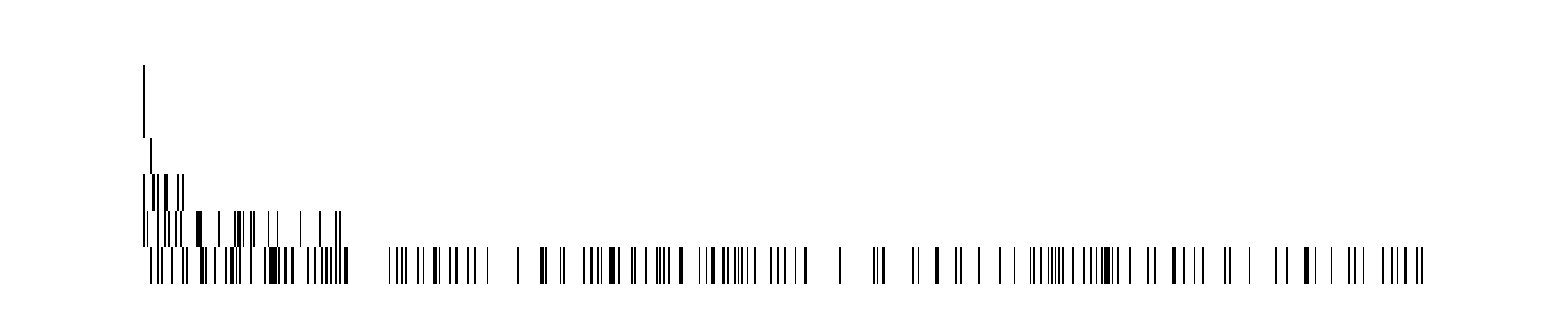

```mathematica
ArrayPlot[Boole[PrimeQ[Map[FromDigits, matA,{2}]]]]
```

```mathematica
Boole[PrimeQ]
```